NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

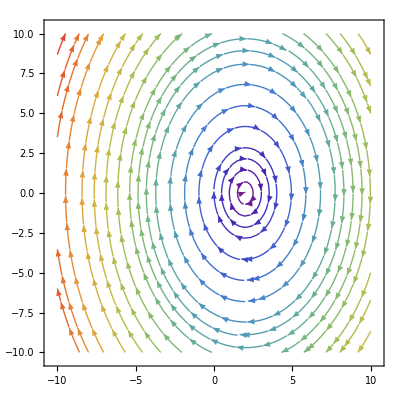

```mathematica
k=2;a=2;
l=2;
T=1;
splot=StreamPlot[{y,-k*(x-l)},{x,-10,10},{y,-10,10},StreamColorFunction->"Rainbow"];
Show[splot,ParametricPlot[Evaluate[First[{x[t],y[t]}/.NDSolve[{x'[t]==y[t],√(a^2+(x[t])^2)==1},{x,y},{t,0,T}]]],{t,0,T},PlotStyle->Red]]
```

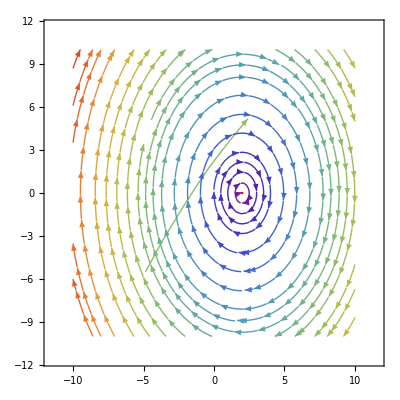

```mathematica
Manipulate[ m={{a1,b1},{a2,b2}};Show[VectorPlot[m.{x,y},{x,-10,10},{y,-10,10},StreamPoints->{{pt1,pt2,pt3,pt4}},StreamStyle->{Red,Thick},ImageSize->{460,310}],Graphics[{Thick,Orange,Map[Line[{-100#,100#}]&,Select[Eigenvectors[m],(Im[#[[1]]]==0&&Im[#[[2]]]==0)&]]}],PlotLabel->Row[{Column[{Row[{Column[{Style["ẋ",Italic],Style["ẏ",Italic]}],Column[{" = "," = "}],TableForm[m.{Style["x",Italic],Style["y",Italic]}]//N}]}],"  ",Column[{"Eigenvalues:",NumberForm[Chop@N@Eigenvalues[m],{4,2}]}],"  ",,Column[{"Eigenvectors:",NumberForm[Chop@N@Eigenvectors[m][[1]],{4,2}],NumberForm[Chop@N@Eigenvectors[m][[2]],{4,2}] }]}]], Style["OverDot[x\]= a_1x + b_1y",Bold], {{a1,1,"a_1"},-10,10,Appearance->"Labeled"}, {{b1,1,"b_1"},-10,10,Appearance->"Labeled"}, Style["ẏ = a_2x + b_2y",Bold], {{a2,2,"a_2"},-10,10,Appearance->"Labeled"},{{b2,-2,"b_2"},-10,10,Appearance->"Labeled"},{{pt1,{-5.1,4.8}},{-10,-10},{10,10},Locator}, {{pt2,{4.9,5.1}},{-10,-10},{10,10},Locator}, {{pt3,{-4.9,-5}},{-10,-10},{10,10},Locator}, {{pt4,{4.9,-5.2}},{-10,-10},{10,10},Locator},TrackedSymbols->True]
```